```mathematica
1+1
```

2

```mathematica
<< MaTeX`
```

```mathematica
fD12 = Import["D:\\Kami\\git_folder\\notes_5sem\\rqc\\data_processing_1\\D12_v1.csv"];
fD12 = Flatten@fD12;
Length@fD12
```

834

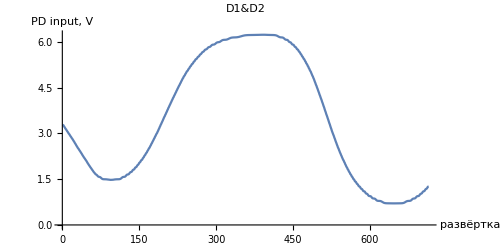

```mathematica
si = 120;
ei = 834;
arrD12 = fD12⟦si;;ei⟧;
scale= 250;
ListPlot[arrD12, PlotRange->Full, Joined->True, ImageSize->{2 scale, scale}, AspectRatio->1/2,
PlotLabel->"D1&D2", AxesLabel->{"развёртка", "PD input, V"}]
```

```mathematica
color1 = RGBColor[0.27,0.25,1.]
```

RGBColor[0.27, 0.25, 1.]

## График

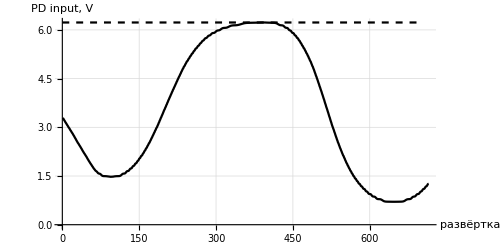

```mathematica
Show[{
ListPlot[arrD12, PlotRange->Full, Joined->True, ImageSize->{2 scale, scale}, AspectRatio->1/2, AxesLabel->{"развёртка", "PD input, V"}, PlotRange->{Automatic, {0, 7}}, GridLines->Automatic, GridLinesStyle -> Opacity[0.1], PlotStyle->Black],
Plot[Max[arrD12], {x, 0, 700}, PlotStyle->{Black, Dashed}]
}]
```

```mathematica
αx = 10. /Length@arrD12;
```

196

94

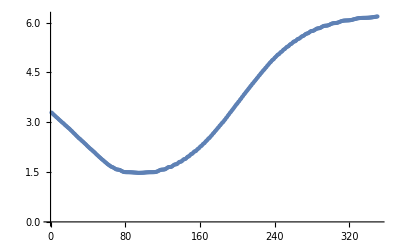

```mathematica
tmp = arrD12⟦;;350⟧;
h1 =Max[tmp]-Min[tmp];
tmp2 = Abs[tmp-(Max[tmp]-h/2)];
val1 = Position[tmp2, Min[tmp2]]⟦1⟧⟦1⟧
Position[tmp, Min[tmp]]⟦1⟧⟦1⟧
ListPlot[tmp]
```

520

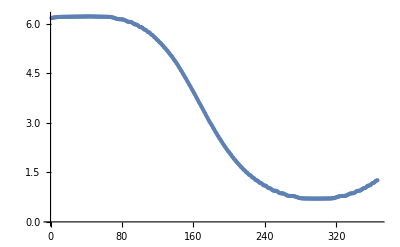

```mathematica
tmp = arrD12⟦350;;⟧;
h2 =Max[tmp]-Min[tmp];
tmp2 = Abs[tmp-(Max[tmp]-h/2)];
val2 = 350+Position[tmp2, Min[tmp2]]⟦1⟧⟦1⟧
ListPlot[tmp]
```

```mathematica
max = 0.34486;
ArrowSize=1.2 10^-2;

m1 = 94;
m2 = 645;
base = arrD12⟦400⟧/max;
min1 = arrD12⟦84⟧;
min2 = arrD12⟦655⟧;
dots2freq=10/(m2-m1);
σ1app = 2Abs[m1-val1]
σ2app = 2Abs[m2-val2]
N[σ1app dots2freq]/2
N[σ2app dots2freq]/2
```

204

250

1.85118

2.2686

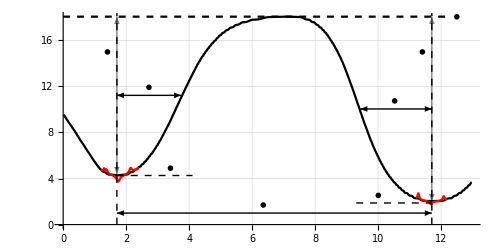

D:\Kami\git_folder\notes_5sem\rqc\data_processing_1\exp_D12.pdf

```mathematica
β = 1.3;
image12 = Show[{
ListPlot[Transpose[{Range[Length[arrD12]]dots2freq, arrD12/max}], PlotRange->Full, Joined->True, ImageSize->{ 2 scale, scale}, AspectRatio->1/2, PlotStyle->Black,AxesLabel->{MaTeX@"\\text{GHz}", MaTeX@"\\text{PD input}"}, PlotRange->{Automatic, {0, 7}}, GridLines->Automatic, GridLinesStyle -> Opacity[0.1], Epilog->{
{Dashed, Line[{{m1 dots2freq, 0},{m1 dots2freq, 20}}]},
{Dashed, Line[{{m2 dots2freq, 0},{m2 dots2freq, 20}}]},
{Dashed, Black, Line[{{m1 dots2freq,  base-1.01h1/max},{m1 dots2freq+2.4, base-1.01h1/max}}]},
{Dashed, Black, Line[{{m2 dots2freq-2.4,  base-1.01h2/max},{m2 dots2freq, base-1.01h2/max}}]},
Arrowheads[{-ArrowSize,ArrowSize}], Arrow[{{m1 dots2freq, base-h1/2/max}, {(m1+1.1σ1app/2)dots2freq, base-h1/2/max}}],
Arrowheads[{-ArrowSize,ArrowSize}], Arrow[{{(m2-σ2app/2)dots2freq, base-h2/2/max}, {m2 dots2freq, base-h2/2/max}}],
Arrowheads[{-ArrowSize,ArrowSize}], Arrow[{{m1 dots2freq,1}, {m2 dots2freq,1}}],
{Opacity[0.5], Arrowheads[{-ArrowSize,ArrowSize}], Arrow[{{m1 dots2freq,base-h1/max}, {m1 dots2freq,base}}]},
{Opacity[0.5],Arrowheads[{-ArrowSize,ArrowSize}], Arrow[{{m2 dots2freq,base-h2/max}, {m2 dots2freq,base}}]},
Text[MaTeX@"\\text{D1}", {m1 dots2freq-0.3, 15}],
Text[MaTeX@"\\text{D2}", {m2 dots2freq-0.3, 15}],
Text[MaTeX@"I_{\\text{out}}[D1]", {m1 dots2freq+1.7, base-h1/max + 1/2}],
Text[MaTeX@"I_{\\text{out}}[D2]", {m2 dots2freq-1.7, base-h2/max + 1/2}],
Text[MaTeX@"I_{\\text{in}}", {12.5, base}],
Text[MaTeX["10.06 \\text{ GHz}"], {350*dots2freq, 1.7}],
Text[MaTeX[ToString[Round[N[σ1app dots2freq]/2, 0.1]]<>"\\text{ GHz}"], {150 * dots2freq,  0.7 + base-h1/2/max}],
Text[MaTeX[ToString[Round[N[σ2app dots2freq]/2, 0.1]]<>"\\text{ GHz}"], {580 * dots2freq,  +0.7 + base-h2/2/max}]
}],
Plot[Max[arrD12]/max, {x, 0, 12.2}, PlotStyle->{Black, Dashed}],
Plot[(a x^2+ b x + c /. fitT1)+β f01[(x -0.2)1000/dots2freqD1], {x, 1.2, 2.4}, PlotRange->All, PlotStyle->Red],
Plot[(a x^2+ b x + c /. fitT2)+β f02[(x -10.8)1000/dots2freqD2], {x, 11.2, 12.2}, PlotRange->All, PlotStyle->Red]
}]
Export[NotebookDirectory[]<>"exp_D12.pdf", image12]
```

## Доп Фит

```mathematica
1/(h1/max)
1/(h2/max)
```

0.0732622

0.0624501

```mathematica
{11., 12.}/dots2freq
```

{606.1,661.2}

```mathematica
fitT1 = FindFit[Transpose[{Range[Length[arrD12]]dots2freq, arrD12/max}]⟦66;;132⟧, {a x^2+ b x + c}, {a, b, c}, x]
```

{a→1.56433,b→-5.45239,c→9.01881}

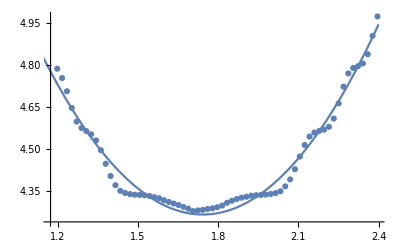

```mathematica
Show[{
ListPlot[Transpose[{Range[Length[arrD12]]dots2freq, arrD12/max}]⟦66;;132⟧],
Plot[a x^2+ b x + c /. fitT1, {x, 1, 2.4}]
}]
```

{a→0.986529,b→-23.1693,c→138.051}

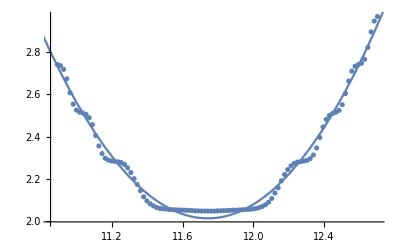

```mathematica
fitT2 = FindFit[Transpose[{Range[Length[arrD12]]dots2freq, arrD12/max}]⟦600;;700⟧, {a x^2+ b x + c}, {a, b, c}, x]
Show[{
ListPlot[Transpose[{Range[Length[arrD12]]dots2freq, arrD12/max}]⟦600;;700⟧],
Plot[a x^2+ b x + c /. fitT2, {x, 10, 13}]
}]
```

## Оценка

```mathematica
kB= 1.38 10^-23;
ℏ = 1.054571817 10^-34;
Na = 6.02 10^23;
R = Na kB;
m = 0.007 / Na;
M = 0.007;
T = 300 + 273;
λ = 671 10^-9;
c = 3 10^8;
```

```mathematica
ν0 = N@(c/λ)
```

4.47094×10^14

```mathematica
ν0 √((8 kB T Log[2])/(m c^2))
```

2.89402×10^9

## Функция

```mathematica
fit02 = {a1->0.3794671171142688,x01->2.6409360533136383,σ1->-0.15903733878099394,a2->-0.19955089661255979,x02->4.858874569572104,σ2->0.25561547935673257,a3->0.2600752341489175,x03->7.078476836791136,σ3->0.18308231983813048,c->-0.021424441811562042};
f02[x_] :=a1 σ1^2/((x-x01)^2+σ1^2)+a2 σ2^2/((x-x02)^2+σ2^2)+a3 σ3^2/((x-x03)^2+σ3^2) /. fit02;
dots2freqD2 = 181.0687583969276;
```

```mathematica
fit01 = {a11->0.2062765611605399,x011->4.0122321204110145,σ11->0.08493480051792772,a12->0.24269808188021735,x012->4.30355657369675,σ12->0.13985216536277725,a2->-0.4120714314265531,x02->5.649390405756049,σ2->0.23869570062971326,a3->0.3268030700140519,x03->7.090911574898094,σ3->0.18216004829338717,c->-0.04176100277561828};
f01[x_] :=a11 σ11^2/((x-x011)^2+σ11^2)+a12 σ12^2/((x-x012)^2+σ12^2)+a2 σ2^2/((x-x02)^2+σ2^2)+a3 σ3^2/((x-x03)^2+σ3^2) /. fit01;
dots2freqD1 = 273.949976281107;
```

```mathematica
f01[1/dots2freqD2]
f02[1/dots2freqD2]
```

-0.000170551

0.000999018

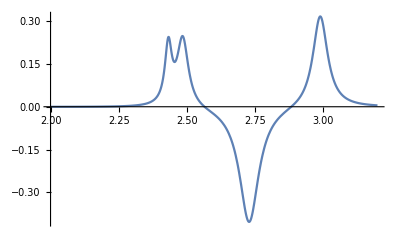

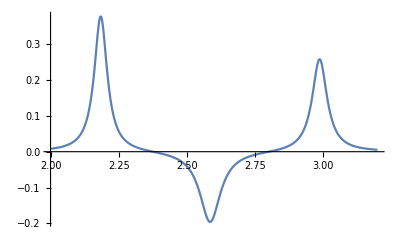

```mathematica
Plot[f01[(x -N[m1 dots2freq ])1000/dots2freqD2], {x, 2, 3.2}, PlotRange->All]
Plot[f02[(x -N[m1 dots2freq ])1000/dots2freqD2], {x, 2, 3.2}, PlotRange->All]
```

## Фит

```mathematica
αx = 1;
xs =αx Range[Length@arrD12] ;
data = Transpose[{xs, Flatten@arrD12}];
```

```mathematica
ClearAll[σ1];
```

{a1→-7.35868,x01→94.0025,σ1→129.936,a2→-8.42087,x02→642.98,σ2→134.251,α→1.,c→9.}

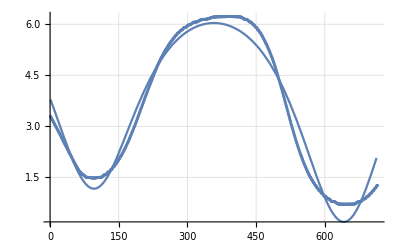

```mathematica
fit = FindFit[data, {
a1 σ1^2/((x-x01)^2+σ1^2) +a2 σ2^2/((x-x02)^2+σ2^2) + c, 0 ≤ c ≤ 9
}, 
{{a1, 0.15}, {x01, 100}, {σ1, 0.12},{a2, 0.18}, {x02, 600}, {σ2, 1},α, {c, 6}}, x]
{aV11, x0V11, σV11, aV12, x0V12, σV12, cV1} = {a1, x01, σ1,a2, x02, σ2, c}/.fit;
f1[x_] := aV11 σV11^2/((x-x0V11)^2+σV11^2) +aV12 σV12^2/((x-x0V12)^2+σV12^2) + cV1;
Show[{
Plot[f1[x], {x, data⟦1⟧⟦1⟧, data⟦ei-si-1⟧⟦1⟧}, PlotRange->All, GridLines->Automatic],
ListPlot[data, PlotRange->All]
}]
```

```mathematica
360+250
```

610

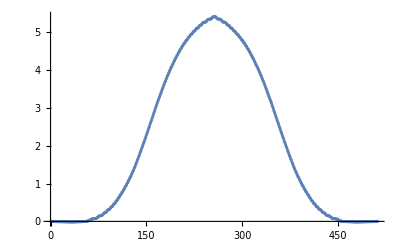

```mathematica
tmp = data⟦360;;360+255, 2⟧;
p2arr= -Join[tmp, Reverse@tmp]+ data⟦360⟧⟦2⟧;
ListPlot[p2arr]
p2data= Transpose[{Range[Length@p2arr], p2arr}];
```